```mathematica
On[Assert]
ClearAll["`*"]
```

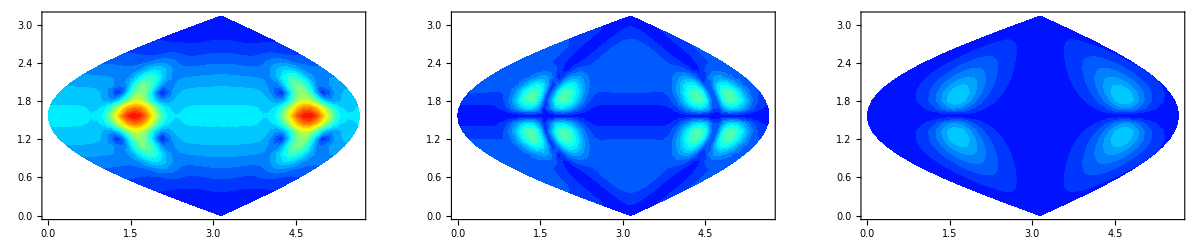

```mathematica
R={x,y,z};
u={0,0,1};
RcrossU=R×u;
RcrossU2=RcrossU.RcrossU;
ϵ=DiagonalMatrix[{1,1,ϵzz}];
ϵu=ϵ0 ϵzz;
ϵuni=ϵ0 ϵ;
rϵ=ϵu R.Inverse[ϵuni].R//Simplify;
gϵuni=ⅇ^(ⅈ k0 Sqrt[rϵ])/(4π Sqrt[rϵ])//Simplify;
rμ=R.R//Simplify;
gμuni=ⅇ^(ⅈ k0 Sqrt[rμ])/(4π Sqrt[rμ])//Simplify;
DelDel[f_]:=Table[D[f,R[[i]],R[[j]]],{i,1,3},{j,1,3}];
B=RcrossU⊗RcrossU/RcrossU2(ϵu/ϵ0 gϵuni-gμuni)+1/(ⅈ k0 RcrossU2)(IdentityMatrix[3]-u⊗u-2RcrossU⊗RcrossU/RcrossU2)(gϵuni Sqrt[rϵ]-gμuni Sqrt[rμ]);
GChen=-B+ϵu Inverse[ϵuni]gϵuni+1/(k0^2)DelDel[gϵuni];
rn=1;
sampleNumber=51;
ϵzzn=6;
margin=8/Sqrt@ϵzzn;
ϕn=Subdivide[Clip[π/2-margin,{0,2π}],Clip[π/2+margin,{0,2π}],sampleNumber];
θn=Subdivide[Clip[π/2-margin/2,{0,π}],Clip[π/2+margin/2,{0,π}],Round[sampleNumber/2]];
k0n=2π;
numeralize[g_]:=Parallelize@Outer[
Function[{θ,ϕ},
N[g/.{y->rn Cos[ϕ]Sin[θ],z->rn Sin[ϕ]Sin[θ],x->rn Cos[θ],ϵzz->ϵzzn,k0->k0n}]
],
θn,ϕn
];
Clear[dimKept];
dimKept=1;
GChen[[;;,2]]=0;
GChen[[;;,3]]=0;
jetColorFunction[x_]:=Blend[{Blue,Cyan,Yellow,Red},x]
plotGreen[g_]:=GraphicsGrid@Transpose@Module[{m},
m=Max[Abs[g]];
Table[
ListContourPlot[Flatten[MapIndexed[
{element,index}|->{(ϕn[[index[[2]]]]-π)Identity[Sin[θn[[index[[1]]]]]]+π,θn[[index[[1]]]],Abs[element[[i,j]]]},
g/m,{2}],1],
AspectRatio->1/2,
ContourLabels->Automatic,
PlotRange->{Automatic,Automatic,{0,1}},
Contours->Subdivide[0,1,21],
ColorFunction->jetColorFunction,
ContourStyle->None,
ColorFunctionScaling->False],
{i,1,3},{j,dimKept,dimKept}]
]
plotGreen@numeralize@GChen
(*d=D[GChen,z,z];
plotGreen@numeralize@d
d=D[d,z];
plotGreen@numeralize@d
d=D[d,z];
plotGreen@numeralize@d
d=D[d,z];
plotGreen@numeralize@d
d=D[GChen,x,x];
plotGreen@numeralize@d
d=D[d,x];
plotGreen@numeralize@d
d=D[d,x];
plotGreen@numeralize@d
d=D[d,x];
plotGreen@numeralize@d*)
```

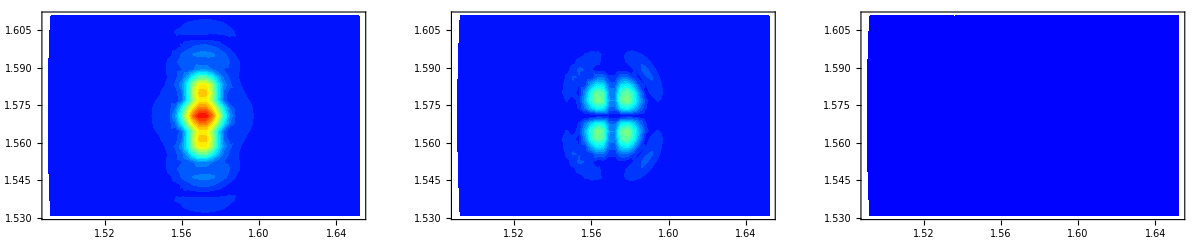

```mathematica
getData[ax_,ay_,az_]:=Module[{rawData,ex,ey,ez,g,linInd},
rawData=Import[FileNameJoin[{NotebookDirectory[],"data","mathematica","eps_"<>ToString@ϵzzn,ToString@ax<>ToString@ay<>ToString@az<>".txt"}],"Table"][[10;;,;;]];
ex=rawData[[;;,4]]+ⅉ rawData[[;;,5]];
ey=rawData[[;;,6]]+ⅉ rawData[[;;,7]];
ez=rawData[[;;,8]]+ⅉ rawData[[;;,9]];
Module[{i=0},Table[i++;
{{ex[[i]],0,0},{ey[[i]],0,0},{ez[[i]],0,0}},{iθ,1,Length@θn},{iϕ,1,Length@ϕn}]
]
]
cartesiansN=Association@Flatten@Table[{ax,ay,az}->getData[ax,ay,az],
{ax,0,maxOrder},{ay,0,Clip[maxOrder-ax,{0,maxOrder}]},{az,0,Clip[maxOrder-ax-ay,{0,maxOrder}]}];
sphericalsN=Association@Flatten@Table[{l,m}->Total@KeyValueMap[{α,value}|->value cartesiansN[α],sphericalToCartesian[{l,m}]],
{l,0,maxOrder},{m,-l,l}];
plotGreen@cartesiansN[{0,0,0}]
```

```mathematica
maxOrder=2;
Clear[cartesians];
cartesians[ax_,ay_,az_]:=cartesians[ax,ay,az]=If[ax>0,
D[cartesians[ax-1,ay,az],x],
If[ay>0,
D[cartesians[ax,ay-1,az],y],
If[az>0,
D[cartesians[ax,ay,az-1],z],
GChen
]]]
Table[cartesians[ax,ay,az],
{ax,0,maxOrder},{ay,0,Clip[maxOrder-ax,{0,maxOrder}]},{az,0,Clip[maxOrder-ax-ay,{0,maxOrder}]}];
ToMultiIndex[coefficient_,powers_]:=If[powers=={},
{},
Total@(UnitVector[3,#]&/@powers)->coefficient]
CoefficientArraysToMultiIndex[array_]:=If[Length@array==1,
<|{0,0,0}->array[[1]]|>,
Association@Select[Flatten@Select[MapIndexed[ToMultiIndex,#,{Length@Dimensions@#}]&/@array,Length@#>0&]/.(index_->0):>{},Length@#>0&]];
dr=dx Sin[θ]Cos[ϕ]+dy Sin[θ]Sin[ϕ]+dz Cos[θ];
sphericalToCartesian=Table[{l,m}->4π(-ⅈ)(-1)^l/k0n^(l+1)
CoefficientArraysToMultiIndex[CoefficientArrays[(dx^2+dy^2+dz^2)^(l/2)Simplify@TrigExpand@ExpToTrig@TransformedField[
"Spherical"->"Cartesian",
SphericalHarmonicY[l,m,θ,ϕ],
{ρ,θ,ϕ}->{dx,dy,dz}
],{dx,dy,dz}]],
{l,0,maxOrder},{m,-l,l}]//Association;
cartesiansN=Association@Flatten@Table[Print[ax,ay,az];{ax,ay,az}->numeralize[cartesians[ax,ay,az]],
{ax,0,maxOrder},{ay,0,Clip[maxOrder-ax,{0,maxOrder}]},{az,0,Clip[maxOrder-ax-ay,{0,maxOrder}]}];
sphericalsN=Association@Flatten@Table[{l,m}->Total@KeyValueMap[{α,value}|->value cartesiansN[α],sphericalToCartesian[{l,m}]],
{l,0,maxOrder},{m,-l,l}];
```

000

001

002

010

011

020

100

101

110

200

```mathematica
g000=cartesiansN[{0,0,0}];
gBaddy=cartesiansN[{0,0,2}];
```

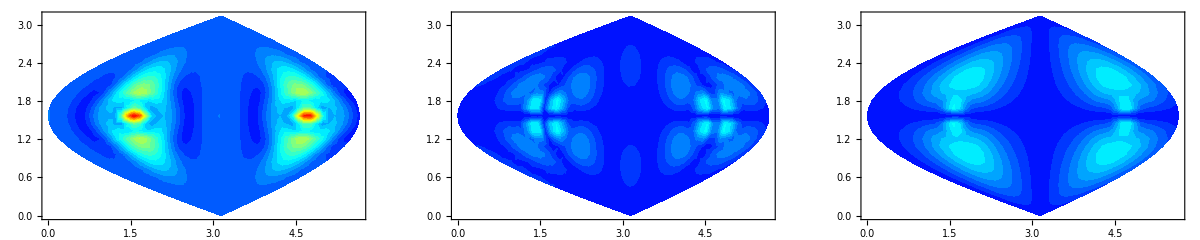

```mathematica
plotGreen@sphericalsN[{2,0}]
```

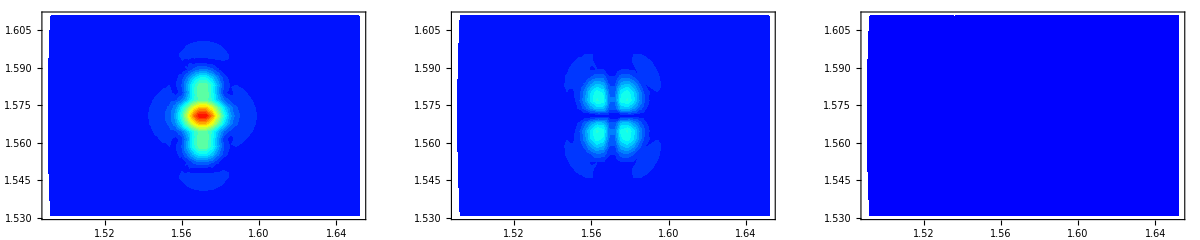

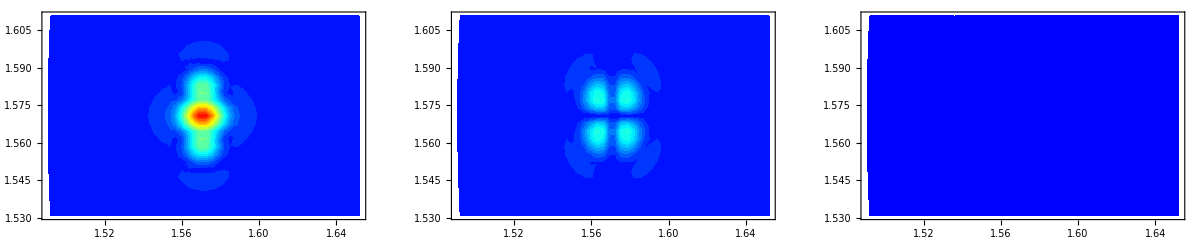

```mathematica
plotGreen@gBaddy
plotGreen[
-1.13/Max@Abs@sphericalsN[{0,0}]sphericalsN[{0,0}](*+0.02sphericalsN[{1,0}]+0(sphericalsN[{2,-2}]+sphericalsN[{2,2}])*)+0.36/Max@Abs@sphericalsN[{2,0}]sphericalsN[{2,0}]
]
```

```mathematica
Max@Abs@gBaddy
69Max@Abs@sphericalsN[{0,0}]
0.02Max@Abs@sphericalsN[{1,0}]
-0.00626Max@Abs@sphericalsN[{2,0}]
```

13661.8

15222.

7.30065

-5019.67

```mathematica
jacobian=Table[Sin[θn[[iθ]]],{iθ,1,Length@θn},{iϕ,1,Length@ϕn},{i,1,3},{j,1,3}];
maxOrder=2;
sphericalNorm[field_]:=Total[Abs[field]^2 jacobian,4]
optimizeCartesian[groundTruth_]:=Module[{cartesianCoeffs},
cartesianCoeffs=Flatten@Table[α[ax,ay,az,real],
{ax,0,maxOrder},{ay,0,Clip[maxOrder-ax,{0,maxOrder}]},{az,0,Clip[maxOrder-ax-ay,{0,maxOrder}]},{real,0,1}];
getCartesianField[coeffsList_]:=Total[If[#[[1]][[4]]==0,1,ⅈ]#[[2]]cartesiansN[#[[1]][[;;3]]]&/@coeffsList,1];
getCartesianError[coeffsList_,truth_]:=
sphericalNorm[getCartesianField[coeffsList]-truth]/sphericalNorm[truth];
formatCartesianOptimizationToNormal[coeffs_]:=Map[varName|->({{#1,#2,#3,#4},varName}&@@varName),coeffs];
cartesianFunToMinimize[coeffs_]:=getCartesianError[formatCartesianOptimizationToNormal[coeffs],groundTruth];
NMinimize[cartesianFunToMinimize@cartesianCoeffs,cartesianCoeffs]
]
optimizeSpherical[groundTruth_]:=Module[{sphericalCoeffs},
sphericalCoeffs=Flatten@Table[α[l,m,real],{l,0,maxOrder},{m,-l,l},{real,0,1}];
getSphericalField[coeffsList_]:=Total[If[#[[1]][[3]]==0,#[[2]],ⅈ#[[2]]]sphericalsN[#[[1]][[;;2]]]&/@coeffsList,1];
getSphericalError[coeffsList_,truth_]:=sphericalNorm[getSphericalField[coeffsList]-truth]/sphericalNorm[truth];
formatSphericalOptimizationToNormal[coeffs_]:=Map[varName|->({{#1,#2,#3},varName}&@@varName),coeffs];
sphericalFunToMinimize[coeffs_]:=getSphericalError[formatSphericalOptimizationToNormal[coeffs],groundTruth];
NMinimize[sphericalFunToMinimize@sphericalCoeffs,sphericalCoeffs]
]
(*resultSpherical=optimizeSpherical[gBaddy]*)
comparison[OptionsPattern[UseParallel->False]]:=Module[{p1,p2},
If[OptionValue[UseParallel],
p1=ParallelSubmit[optimizeCartesian[gBaddy]];
p2=ParallelSubmit[optimizeSpherical[gBaddy]];
WaitAll[{p1,p2}],
{optimizeCartesian[truth],optimizeSpherical[truth]}
]
]
result=comparison[UseParallel->True];
```

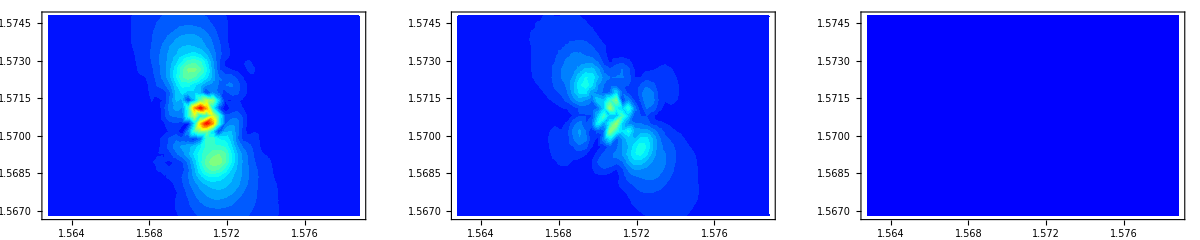

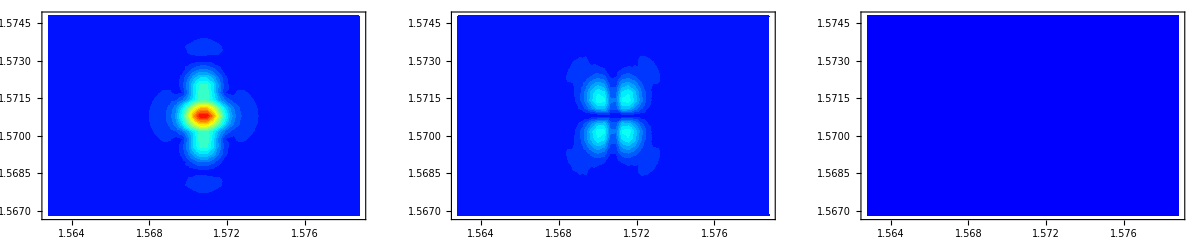

548.439

20.835

```mathematica
(*αGroundTruth=Keys[Association@processedData[[ind]]][[1]]*)
greenCartesian=getCartesianField@KeyValueMap[{key,value}|->{(({#1,#2,#3,#4}&@@key)),value},Association[result[[1]][[2]]]];
greenSpherical=getSphericalField@KeyValueMap[{key,value}|->{(({#1,#2,#3}&@@key)),value},Association[result[[2]][[2]]]];
plotGreen@greenCartesian
plotGreen@greenSpherical
Sqrt[result[[1]][[1]]]100
Sqrt[result[[2]][[1]]]100
```

```mathematica
1.7Max@Abs@sphericalsN[{0,0}]/Max@Abs@gBaddy 
2.97 Max@Abs@sphericalsN[{1,0}]/Max@Abs@gBaddy 
0.00031325Max@Abs@sphericalsN[{2,0}]/Max@Abs@gBaddy
```

0.274243

0.79278

0.183678

```mathematica
result[[2]][[2]]
```

{α[0,0,0]→-0.0264683,α[0,0,1]→-1.70264,α[1,-1,0]→5.14146×10^-8,α[1,-1,1]→-5.47805×10^-7,α[1,0,0]→2.97698,α[1,0,1]→0.000599736,α[1,1,0]→2.52218×10^-8,α[1,1,1]→-5.34201×10^-7,α[2,-2,0]→1.4155×10^-7,α[2,-2,1]→-6.96397×10^-8,α[2,-1,0]→-5.3698×10^-7,α[2,-1,1]→-1.7529×10^-7,α[2,0,0]→7.51858×10^-7,α[2,0,1]→0.000313256,α[2,1,0]→-5.64147×10^-7,α[2,1,1]→-2.28557×10^-7,α[2,2,0]→1.41558×10^-7,α[2,2,1]→-6.96305×10^-8}

```mathematica
gTest=Simplify[TransformedField["Cartesian"->"Spherical",D[GChen[[1,1]],z,z]/.{k0->k0n,ϵzz->1},R->{ρ,θ,ϕ}]/.ρ->rn];
```

```mathematica
groundTruthNorm=sphericalInt[Abs[gTest]^2];
sphericalInt[expr_]:=NIntegrate[expr Sin[θ],{θ,0,π},{ϕ,0,2π},
AccuracyGoal->7,PrecisionGoal->4,WorkingPrecision->50,MaxRecursion->20,Method->"GaussKronrodRule"]
lMax=12;
projectionResult=Flatten[Parallelize@Table[{l,m,sphericalInt[Conjugate[SphericalHarmonicY[l,m,θ,ϕ]]gTest]
},
{l,0,lMax},{m,-l,l}
],1];
projectionResult=Map[If[Abs@#<1*^-12,0,#]&,projectionResult,{
If[Length@gTest==1,2,3]
}];
```

```mathematica
plotResult=ParallelTable[{lMaxProj,Module[{GChenNumSpherical,error},
GChenNumSpherical=Total@Map[Function[{l,m,p},
If[l<=lMaxProj,
SphericalHarmonicY[l,m,θ,ϕ]p ,
0
]
]@@#&,projectionResult,{1}];
(*Print@GChenNumSpherical*)
error=sphericalInt[Total@Abs[GChenNumSpherical-gTest]^2]/groundTruthNorm 100
]},{lMaxProj,0,lMax}];
```

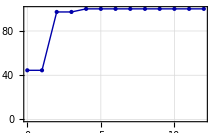

```mathematica
plot=ListPlot[Map[{#[[1]],100-#[[2]]}&,plotResult],
PlotRange->Full,
Joined->True,
PlotStyle->{Darker@Blue,Thick},
Frame->True,
PlotRange->{{0,lMax},{0,100}},
Mesh->All,
MeshStyle->{PointSize[Medium]},
FrameStyle->Directive[Black],
GridLines->Automatic,
BaseStyle->{FontFamily->"Times New Roman",FontSize->10},
ImageSize->{72 3,Automatic}
]
Export[FileNameJoin[{NotebookDirectory[],"..","figs","export.svg"}],plot];
```

```mathematica
Coefficient[Simplify[TransformedField["Cartesian"->"Cylindrical", GChen[[1,1]],R->{ρ,ϕ,zc}]]//Expand,ϵzz]
```

-(ⅇ^(ⅈ k0 √(zc^2+ϵzz ρ^2)) zc^2)/(4 k0^2 π (zc^2+ϵzz ρ^2)^(5/2))+(ⅇ^(ⅈ k0 √(zc^2+ϵzz ρ^2)) zc^4)/(8 π (zc^2+ϵzz ρ^2)^(5/2))+(ⅇ^(ⅈ k0 √(zc^2+ϵzz ρ^2)) zc^4 Cos[2 ϕ])/(8 π (zc^2+ϵzz ρ^2)^(5/2))

```mathematica
toSphericalTfm=MapThread[#1->#2&,{R,CoordinateTransformData["Spherical"->"Cartesian","Mapping"][{r,θ,ϕ}]}];
ϵzzn=1000^2;
subs={k0->k0n,ϵzz->ϵzzn,r->1,ρ->Sin[θ]};
g0=Exp[ⅉ k0 Sqrt[x^2+y^2+z^2]]/(4π  Sqrt[x^2+y^2+z^2]);
h0=-(ⅈ ⅇ^(ⅈ k0 z) ExpIntegralEi[ⅈ k0 (-z+√(x^2+y^2+z^2))])/(8 k0 π)-(ⅈ ⅇ^(-ⅈ k0 z) ExpIntegralEi[ⅈ k0 (z+√(x^2+y^2+z^2))])/(8 k0 π)(*-(ⅈ ⅇ^(-ⅈ k0 Abs@ z) Log[x^2+y^2])/(8 k0 π)*);
(*h0=(Exp[-1/2/(x^2+y^2)/ϵzz]/Sqrt@ϵzz Sin[k0 z])/k0;*)
GChenLar={{(-k0^2h0-D[h0,x,x]-D[h0,z,z])//Simplify,0,0},{-D[h0,x,y]//Simplify,0,0},{0,0,0}};
(*re=Sqrt[ϵzz]ρ;
c={0,0,1};
iTransverse=DiagonalMatrix[{1,1,0}];
ϵinvϵ=ϵzz iTransverse;
expTerm=Exp[ⅉ k0 re]/re;
GLar=-ϵzz Exp[ⅉ k0 re/2]/re Sin[k0 re/2]/(k0 re/2)(
IdentityMatrix[3]-c⊗c-2(R×c)⊗(R×c)/ρ^2
);
GChenLar=(1/(4π)GLar/.ρ->Sqrt[x^2+y^2]);*)
(*GChenLar={{ϵzz^2 Simplify@TransformedField["Cylindrical"->"Cartesian",Coefficient[Expand@Simplify[TransformedField["Cartesian"->"Cylindrical", GChen[[1,1]],R->{ρ,ϕ,zc}]],ϵzz^(1)],{ρ,ϕ,zc}->R],0,0},{0,0,0},{0,0,0}};*)
(*GChenLar={{ϵzz^1Simplify@ Coefficient[GChen[[1,1]],ϵzz^1],0,0},{0,0,0},{0,0,0}};*)
(*GChenLar={{Log[x^2+y^2]Sin[ϵzzn z]Sign[z],0,0},{0,0,0},{0,0,0}};*)
GChenSphere=Simplify[GChen/.toSphericalTfm/.subs];
GChenLarSphere=Simplify[GChenLar/.toSphericalTfm/.subs]/.{Sign'[x_]:>2DiracDelta[x],Sign''[x_]:>2DiracDelta'[x]}
smoothSymmetricStep=(Erf[ϵzzn θ-2]+Erf[ϵzzn(π-θ)-2])/2;
```

{{((2 π-2 π Cos[2 θ]+π Cos[2 θ-2 ϕ]-4 ⅈ Cos[2 ϕ]-2 π Cos[2 ϕ]+π Cos[2 (θ+ϕ)]) Csc[θ]^2)/(32 π^2),0,0},{((-2 ⅈ-π+π Cos[2 θ]) Csc[θ]^2 Sin[2 ϕ])/(16 π^2),0,0},{0,0,0}}

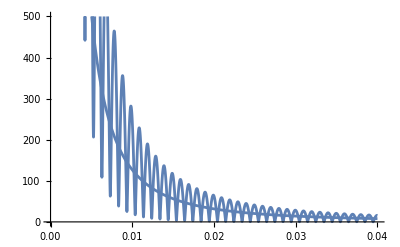

```mathematica
plotLine[expr_]:=Module[{p},p=expr[[1,1]]/.ϕ->0;
Plot[Abs@p,{θ,1/100/20,4/100/1},PlotRange->{0,10000/20}]
]
Show[plotLine[GChenSphere],
plotLine[GChenLarSphere ]]
```

299.704

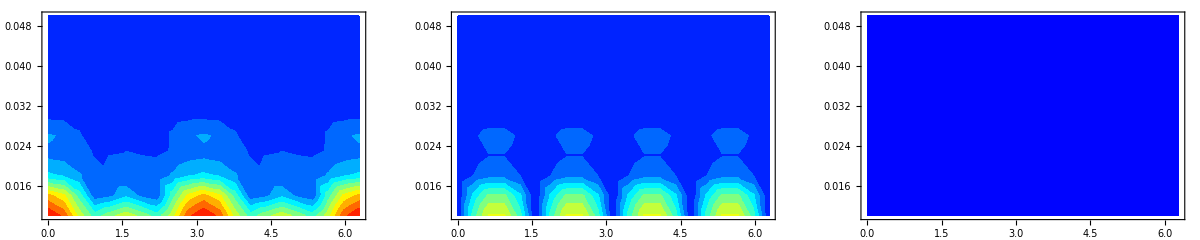

253.311

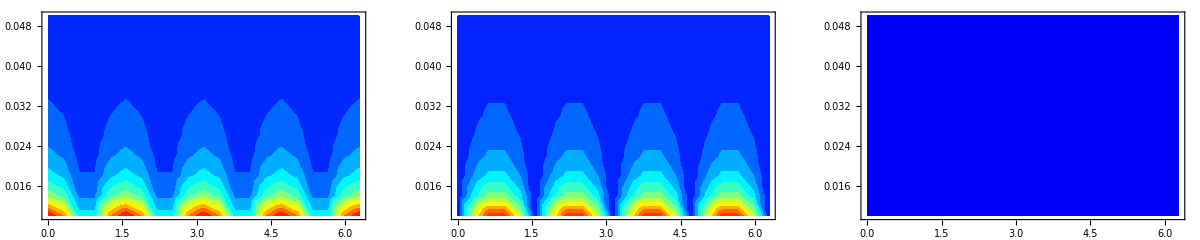

```mathematica
sampleNumber=20;
margin=1*^-2;
ϕn=Subdivide[0,2π,sampleNumber];
θn=Subdivide[1/Sqrt@ϵzzn,5/Sqrt@ϵzzn/1,sampleNumber/2];
numeralize[g_]:=Parallelize@Outer[
Function[{θ,ϕ},
N[g/.{x->rn Cos[ϕ]Sin[θ],y->rn Sin[ϕ]Sin[θ],z->rn Cos[θ],ϵzz->ϵzzn,k0->k0n}]
],
θn,ϕn
];
plotGreen[g_]:=GraphicsGrid@Transpose@Module[{m},
m=Max[Abs[g]];
Print@m;
Table[
ListContourPlot[Flatten[MapIndexed[
{element,index}|->{ϕn[[index[[2]]]],θn[[index[[1]]]],Abs[element[[i,j]]]},
g/m,{2}],1],
AspectRatio->1/2,
ContourLabels->Automatic,
PlotRange->{{0,2π},{Min@θn,Max@θn},{0,1}},
Contours->Subdivide[0,1,11],
ColorFunction->jetColorFunction,
ContourStyle->None,
ColorFunctionScaling->False
],
{i,1,3},{j,dimKept,dimKept}]
]
GChen[[;;,2;;]]=0;
plotGreen@numeralize@GChen
plotGreen@numeralize@(2GChenLar)
```

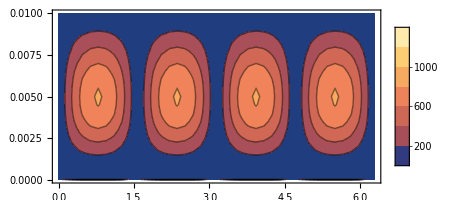

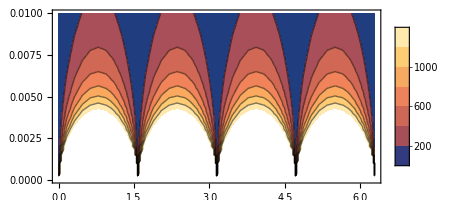

```mathematica
iPlot=2;
jPlot=1;
singularPlot[expr_]:=ContourPlot[Abs@expr[[iPlot,jPlot]],{ϕ,0,2π},{θ,0,.01},MaxRecursion->0,PlotPoints->{41,21},AspectRatio->1/2,PlotRange->{0,1400},PlotLegends->Automatic]
singularPlot[GChenSphere]
singularPlot[GChenLarSphere]
(*(*margin=1*^-6;*)
margin=.1/180π;
sphericalInt[expr_]:=NIntegrate[smoothSymmetricStep expr Sin[θ],{θ,margin,π-margin},{ϕ,0,2π},
AccuracyGoal->7,PrecisionGoal->4,WorkingPrecision->50,MaxRecursion->20,Method->"GaussKronrodRule"];
ParallelTable[Module[{GChenSphereNorm},
GChenSphereNorm=sphericalInt[Abs[GChenSphere[[iPlot,jPlot]]]^2];
If[GChenSphereNorm>1*^-6,
sphericalInt[Abs[GChenLarSphere[[iPlot,jPlot]]-GChenSphere[[iPlot,jPlot]]]^2]/GChenSphereNorm 100,
0]],
{iPlot,1,3},{jPlot,1,1},Method->"CoarsestGrained"]*)
```

```mathematica
saveToFile[α_]:=Module[{filename,fd,toExport},
filename=FileNameJoin[{NotebookDirectory[],"data","mathematica","eps_"<>ToString@ϵzzn<>"/"<>ToString@α[[1]]<>ToString@α[[2]]<>ToString@α[[3]]<>".txt"}];
fd=OpenWrite[filename];
Table[WriteString[filename,"This line empty on purpose\n"],{i,1,9}];
Close[fd];
fd=OpenAppend[filename];
toExport=cartesiansN[α];
Table[
WriteString[filename,
ToString[N[rn Cos[θn[[i]]]],CForm]<>" "<>
ToString[N[rn Cos[ϕn[[j]]]Sin[θn[[i]]]],CForm]<>" "<>
ToString[N[rn Sin[ϕn[[j]]]Sin[θn[[i]]]],CForm]<>" "<>
ToString[N[Re@toExport[[i,j,1,1]]],CForm]<>" "<>
ToString[N[Im@toExport[[i,j,1,1]]],CForm]<>" "<>
ToString[N[Re@toExport[[i,j,2,1]]],CForm]<>" "<>
ToString[N[Im@toExport[[i,j,2,1]]],CForm]<>" "<>
ToString[N[Re@toExport[[i,j,3,1]]],CForm]<>" "<>
ToString[N[Im@toExport[[i,j,3,1]]],CForm]<>" "<>
"\n"],
{i,1,Length@θn},{j,1,Length@ϕn}];
Close@fd;
]
Table[saveToFile[{ax,ay,az}],
{ax,0,maxOrder},{ay,0,Clip[maxOrder-ax,{0,maxOrder}]},{az,0,Clip[maxOrder-ax-ay,{0,maxOrder}]}];
```

```mathematica
sphericalToCartesian[{1,-1}]
```

<|{1,0,0}→(ⅈ √(3/2))/(2 π^(3/2)),{0,1,0}→(√(3/2))/(2 π^(3/2))|>

```mathematica
KeyValueMap[{lm,assoc}|->Module[{},ToString@lm<>":\n{"<>
KeyValueMap[{α,coeff}|->ToString[α]<>":"<>ToString[coeff,CForm]<>",\n"
,assoc]<>"}"],
sphericalToCartesian]
```

{{0, 0}:
{{0, 0, 0}:Complex(0,-1)/Sqrt(Pi),
},{1, -1}:
{{1, 0, 0}:(Complex(0,0.5)*Sqrt(1.5))/Power(Pi,1.5),
{0, 1, 0}:Sqrt(1.5)/(2.*Power(Pi,1.5)),
},{1, 0}:
{{0, 0, 1}:(Complex(0,0.5)*Sqrt(3))/Power(Pi,1.5),
},{1, 1}:
{{1, 0, 0}:(Complex(0,-0.5)*Sqrt(1.5))/Power(Pi,1.5),
{0, 1, 0}:Sqrt(1.5)/(2.*Power(Pi,1.5)),
},{2, -2}:
{{2, 0, 0}:(Complex(0,-0.125)*Sqrt(7.5))/Power(Pi,2.5),
{1, 1, 0}:-0.25*Sqrt(7.5)/Power(Pi,2.5),
{0, 2, 0}:(Complex(0,0.125)*Sqrt(7.5))/Power(Pi,2.5),
},{2, -1}:
{{1, 0, 1}:(Complex(0,-0.25)*Sqrt(7.5))/Power(Pi,2.5),
{0, 1, 1}:-0.25*Sqrt(7.5)/Power(Pi,2.5),
},{2, 0}:
{{2, 0, 0}:(Complex(0,0.125)*Sqrt(5))/Power(Pi,2.5),
{0, 2, 0}:(Complex(0,0.125)*Sqrt(5))/Power(Pi,2.5),
{0, 0, 2}:(Complex(0,-0.25)*Sqrt(5))/Power(Pi,2.5),
},{2, 1}:
{{1, 0, 1}:(Complex(0,0.25)*Sqrt(7.5))/Power(Pi,2.5),
{0, 1, 1}:-0.25*Sqrt(7.5)/Power(Pi,2.5),
},{2, 2}:
{{2, 0, 0}:(Complex(0,-0.125)*Sqrt(7.5))/Power(Pi,2.5),
{1, 1, 0}:Sqrt(7.5)/(4.*Power(Pi,2.5)),
{0, 2, 0}:(Complex(0,0.125)*Sqrt(7.5))/Power(Pi,2.5),
},{3, -3}:
{{3, 0, 0}:(Complex(0,0.03125)*Sqrt(35))/Power(Pi,3.5),
{2, 1, 0}:(3*Sqrt(35))/(32.*Power(Pi,3.5)),
{1, 2, 0}:(Complex(0,-0.09375)*Sqrt(35))/Power(Pi,3.5),
{0, 3, 0}:-0.03125*Sqrt(35)/Power(Pi,3.5),
},{3, -2}:
{{2, 0, 1}:(Complex(0,0.0625)*Sqrt(52.5))/Power(Pi,3.5),
{1, 1, 1}:Sqrt(52.5)/(8.*Power(Pi,3.5)),
{0, 2, 1}:(Complex(0,-0.0625)*Sqrt(52.5))/Power(Pi,3.5),
},{3, -1}:
{{3, 0, 0}:(Complex(0,-0.03125)*Sqrt(21))/Power(Pi,3.5),
{2, 1, 0}:-0.03125*Sqrt(21)/Power(Pi,3.5),
{1, 2, 0}:(Complex(0,-0.03125)*Sqrt(21))/Power(Pi,3.5),
{1, 0, 2}:(Complex(0,0.125)*Sqrt(21))/Power(Pi,3.5),
{0, 3, 0}:-0.03125*Sqrt(21)/Power(Pi,3.5),
{0, 1, 2}:Sqrt(21)/(8.*Power(Pi,3.5)),
},{3, 0}:
{{2, 0, 1}:(Complex(0,-0.1875)*Sqrt(7))/Power(Pi,3.5),
{0, 2, 1}:(Complex(0,-0.1875)*Sqrt(7))/Power(Pi,3.5),
{0, 0, 3}:(Complex(0,0.125)*Sqrt(7))/Power(Pi,3.5),
},{3, 1}:
{{3, 0, 0}:(Complex(0,0.03125)*Sqrt(21))/Power(Pi,3.5),
{2, 1, 0}:-0.03125*Sqrt(21)/Power(Pi,3.5),
{1, 2, 0}:(Complex(0,0.03125)*Sqrt(21))/Power(Pi,3.5),
{1, 0, 2}:(Complex(0,-0.125)*Sqrt(21))/Power(Pi,3.5),
{0, 3, 0}:-0.03125*Sqrt(21)/Power(Pi,3.5),
{0, 1, 2}:Sqrt(21)/(8.*Power(Pi,3.5)),
},{3, 2}:
{{2, 0, 1}:(Complex(0,0.0625)*Sqrt(52.5))/Power(Pi,3.5),
{1, 1, 1}:-0.125*Sqrt(52.5)/Power(Pi,3.5),
{0, 2, 1}:(Complex(0,-0.0625)*Sqrt(52.5))/Power(Pi,3.5),
},{3, 3}:
{{3, 0, 0}:(Complex(0,-0.03125)*Sqrt(35))/Power(Pi,3.5),
{2, 1, 0}:(3*Sqrt(35))/(32.*Power(Pi,3.5)),
{1, 2, 0}:(Complex(0,0.09375)*Sqrt(35))/Power(Pi,3.5),
{0, 3, 0}:-0.03125*Sqrt(35)/Power(Pi,3.5),
},{4, -4}:
{{4, 0, 0}:(Complex(0,-0.0234375)*Sqrt(17.5))/Power(Pi,4.5),
{3, 1, 0}:(-3*Sqrt(17.5))/(32.*Power(Pi,4.5)),
{2, 2, 0}:(Complex(0,0.140625)*Sqrt(17.5))/Power(Pi,4.5),
{1, 3, 0}:(3*Sqrt(17.5))/(32.*Power(Pi,4.5)),
{0, 4, 0}:(Complex(0,-0.0234375)*Sqrt(17.5))/Power(Pi,4.5),
},{4, -3}:
{{3, 0, 1}:(Complex(0,-0.046875)*Sqrt(35))/Power(Pi,4.5),
{2, 1, 1}:(-9*Sqrt(35))/(64.*Power(Pi,4.5)),
{1, 2, 1}:(Complex(0,0.140625)*Sqrt(35))/Power(Pi,4.5),
{0, 3, 1}:(3*Sqrt(35))/(64.*Power(Pi,4.5)),
},{4, -2}:
{{4, 0, 0}:(Complex(0,0.046875)*Sqrt(2.5))/Power(Pi,4.5),
{3, 1, 0}:(3*Sqrt(2.5))/(32.*Power(Pi,4.5)),
{2, 0, 2}:(Complex(0,-0.28125)*Sqrt(2.5))/Power(Pi,4.5),
{1, 3, 0}:(3*Sqrt(2.5))/(32.*Power(Pi,4.5)),
{1, 1, 2}:(-9*Sqrt(2.5))/(16.*Power(Pi,4.5)),
{0, 4, 0}:(Complex(0,-0.046875)*Sqrt(2.5))/Power(Pi,4.5),
{0, 2, 2}:(Complex(0,0.28125)*Sqrt(2.5))/Power(Pi,4.5),
},{4, -1}:
{{3, 0, 1}:(Complex(0,0.140625)*Sqrt(5))/Power(Pi,4.5),
{2, 1, 1}:(9*Sqrt(5))/(64.*Power(Pi,4.5)),
{1, 2, 1}:(Complex(0,0.140625)*Sqrt(5))/Power(Pi,4.5),
{1, 0, 3}:(Complex(0,-0.1875)*Sqrt(5))/Power(Pi,4.5),
{0, 3, 1}:(9*Sqrt(5))/(64.*Power(Pi,4.5)),
{0, 1, 3}:(-3*Sqrt(5))/(16.*Power(Pi,4.5)),
},{4, 0}:
{{4, 0, 0}:Complex(0,-0.0703125)/Power(Pi,4.5),
{2, 2, 0}:Complex(0,-0.140625)/Power(Pi,4.5),
{2, 0, 2}:Complex(0,0.5625)/Power(Pi,4.5),
{0, 4, 0}:Complex(0,-0.0703125)/Power(Pi,4.5),
{0, 2, 2}:Complex(0,0.5625)/Power(Pi,4.5),
{0, 0, 4}:Complex(0,-0.1875)/Power(Pi,4.5),
},{4, 1}:
{{3, 0, 1}:(Complex(0,-0.140625)*Sqrt(5))/Power(Pi,4.5),
{2, 1, 1}:(9*Sqrt(5))/(64.*Power(Pi,4.5)),
{1, 2, 1}:(Complex(0,-0.140625)*Sqrt(5))/Power(Pi,4.5),
{1, 0, 3}:(Complex(0,0.1875)*Sqrt(5))/Power(Pi,4.5),
{0, 3, 1}:(9*Sqrt(5))/(64.*Power(Pi,4.5)),
{0, 1, 3}:(-3*Sqrt(5))/(16.*Power(Pi,4.5)),
},{4, 2}:
{{4, 0, 0}:(Complex(0,0.046875)*Sqrt(2.5))/Power(Pi,4.5),
{3, 1, 0}:(-3*Sqrt(2.5))/(32.*Power(Pi,4.5)),
{2, 0, 2}:(Complex(0,-0.28125)*Sqrt(2.5))/Power(Pi,4.5),
{1, 3, 0}:(-3*Sqrt(2.5))/(32.*Power(Pi,4.5)),
{1, 1, 2}:(9*Sqrt(2.5))/(16.*Power(Pi,4.5)),
{0, 4, 0}:(Complex(0,-0.046875)*Sqrt(2.5))/Power(Pi,4.5),
{0, 2, 2}:(Complex(0,0.28125)*Sqrt(2.5))/Power(Pi,4.5),
},{4, 3}:
{{3, 0, 1}:(Complex(0,0.046875)*Sqrt(35))/Power(Pi,4.5),
{2, 1, 1}:(-9*Sqrt(35))/(64.*Power(Pi,4.5)),
{1, 2, 1}:(Complex(0,-0.140625)*Sqrt(35))/Power(Pi,4.5),
{0, 3, 1}:(3*Sqrt(35))/(64.*Power(Pi,4.5)),
},{4, 4}:
{{4, 0, 0}:(Complex(0,-0.0234375)*Sqrt(17.5))/Power(Pi,4.5),
{3, 1, 0}:(3*Sqrt(17.5))/(32.*Power(Pi,4.5)),
{2, 2, 0}:(Complex(0,0.140625)*Sqrt(17.5))/Power(Pi,4.5),
{1, 3, 0}:(-3*Sqrt(17.5))/(32.*Power(Pi,4.5)),
{0, 4, 0}:(Complex(0,-0.0234375)*Sqrt(17.5))/Power(Pi,4.5),
},{5, -5}:
{{5, 0, 0}:(Complex(0,0.005859375)*Sqrt(77))/Power(Pi,5.5),
{4, 1, 0}:(15*Sqrt(77))/(512.*Power(Pi,5.5)),
{3, 2, 0}:(Complex(0,-0.05859375)*Sqrt(77))/Power(Pi,5.5),
{2, 3, 0}:(-15*Sqrt(77))/(256.*Power(Pi,5.5)),
{1, 4, 0}:(Complex(0,0.029296875)*Sqrt(77))/Power(Pi,5.5),
{0, 5, 0}:(3*Sqrt(77))/(512.*Power(Pi,5.5)),
},{5, -4}:
{{4, 0, 1}:(Complex(0,0.01171875)*Sqrt(192.5))/Power(Pi,5.5),
{3, 1, 1}:(3*Sqrt(192.5))/(64.*Power(Pi,5.5)),
{2, 2, 1}:(Complex(0,-0.0703125)*Sqrt(192.5))/Power(Pi,5.5),
{1, 3, 1}:(-3*Sqrt(192.5))/(64.*Power(Pi,5.5)),
{0, 4, 1}:(Complex(0,0.01171875)*Sqrt(192.5))/Power(Pi,5.5),
},{5, -3}:
{{5, 0, 0}:(Complex(0,-0.001953125)*Sqrt(385))/Power(Pi,5.5),
{4, 1, 0}:(-3*Sqrt(385))/(512.*Power(Pi,5.5)),
{3, 2, 0}:(Complex(0,0.00390625)*Sqrt(385))/Power(Pi,5.5),
{3, 0, 2}:(Complex(0,0.015625)*Sqrt(385))/Power(Pi,5.5),
{2, 3, 0}:-0.00390625*Sqrt(385)/Power(Pi,5.5),
{2, 1, 2}:(3*Sqrt(385))/(64.*Power(Pi,5.5)),
{1, 4, 0}:(Complex(0,0.005859375)*Sqrt(385))/Power(Pi,5.5),
{1, 2, 2}:(Complex(0,-0.046875)*Sqrt(385))/Power(Pi,5.5),
{0, 5, 0}:Sqrt(385)/(512.*Power(Pi,5.5)),
{0, 3, 2}:-0.015625*Sqrt(385)/Power(Pi,5.5),
},{5, -2}:
{{4, 0, 1}:(Complex(0,-0.0078125)*Sqrt(577.5))/Power(Pi,5.5),
{3, 1, 1}:-0.015625*Sqrt(577.5)/Power(Pi,5.5),
{2, 0, 3}:(Complex(0,0.015625)*Sqrt(577.5))/Power(Pi,5.5),
{1, 3, 1}:-0.015625*Sqrt(577.5)/Power(Pi,5.5),
{1, 1, 3}:Sqrt(577.5)/(32.*Power(Pi,5.5)),
{0, 4, 1}:(Complex(0,0.0078125)*Sqrt(577.5))/Power(Pi,5.5),
{0, 2, 3}:(Complex(0,-0.015625)*Sqrt(577.5))/Power(Pi,5.5),
},{5, -1}:
{{5, 0, 0}:(Complex(0,0.00390625)*Sqrt(82.5))/Power(Pi,5.5),
{4, 1, 0}:Sqrt(82.5)/(256.*Power(Pi,5.5)),
{3, 2, 0}:(Complex(0,0.0078125)*Sqrt(82.5))/Power(Pi,5.5),
{3, 0, 2}:(Complex(0,-0.046875)*Sqrt(82.5))/Power(Pi,5.5),
{2, 3, 0}:Sqrt(82.5)/(128.*Power(Pi,5.5)),
{2, 1, 2}:(-3*Sqrt(82.5))/(64.*Power(Pi,5.5)),
{1, 4, 0}:(Complex(0,0.00390625)*Sqrt(82.5))/Power(Pi,5.5),
{1, 2, 2}:(Complex(0,-0.046875)*Sqrt(82.5))/Power(Pi,5.5),
{1, 0, 4}:(Complex(0,0.03125)*Sqrt(82.5))/Power(Pi,5.5),
{0, 5, 0}:Sqrt(82.5)/(256.*Power(Pi,5.5)),
{0, 3, 2}:(-3*Sqrt(82.5))/(64.*Power(Pi,5.5)),
{0, 1, 4}:Sqrt(82.5)/(32.*Power(Pi,5.5)),
},{5, 0}:
{{4, 0, 1}:(Complex(0,0.05859375)*Sqrt(11))/Power(Pi,5.5),
{2, 2, 1}:(Complex(0,0.1171875)*Sqrt(11))/Power(Pi,5.5),
{2, 0, 3}:(Complex(0,-0.15625)*Sqrt(11))/Power(Pi,5.5),
{0, 4, 1}:(Complex(0,0.05859375)*Sqrt(11))/Power(Pi,5.5),
{0, 2, 3}:(Complex(0,-0.15625)*Sqrt(11))/Power(Pi,5.5),
{0, 0, 5}:(Complex(0,0.03125)*Sqrt(11))/Power(Pi,5.5),
},{5, 1}:
{{5, 0, 0}:(Complex(0,-0.00390625)*Sqrt(82.5))/Power(Pi,5.5),
{4, 1, 0}:Sqrt(82.5)/(256.*Power(Pi,5.5)),
{3, 2, 0}:(Complex(0,-0.0078125)*Sqrt(82.5))/Power(Pi,5.5),
{3, 0, 2}:(Complex(0,0.046875)*Sqrt(82.5))/Power(Pi,5.5),
{2, 3, 0}:Sqrt(82.5)/(128.*Power(Pi,5.5)),
{2, 1, 2}:(-3*Sqrt(82.5))/(64.*Power(Pi,5.5)),
{1, 4, 0}:(Complex(0,-0.00390625)*Sqrt(82.5))/Power(Pi,5.5),
{1, 2, 2}:(Complex(0,0.046875)*Sqrt(82.5))/Power(Pi,5.5),
{1, 0, 4}:(Complex(0,-0.03125)*Sqrt(82.5))/Power(Pi,5.5),
{0, 5, 0}:Sqrt(82.5)/(256.*Power(Pi,5.5)),
{0, 3, 2}:(-3*Sqrt(82.5))/(64.*Power(Pi,5.5)),
{0, 1, 4}:Sqrt(82.5)/(32.*Power(Pi,5.5)),
},{5, 2}:
{{4, 0, 1}:(Complex(0,-0.0078125)*Sqrt(577.5))/Power(Pi,5.5),
{3, 1, 1}:Sqrt(577.5)/(64.*Power(Pi,5.5)),
{2, 0, 3}:(Complex(0,0.015625)*Sqrt(577.5))/Power(Pi,5.5),
{1, 3, 1}:Sqrt(577.5)/(64.*Power(Pi,5.5)),
{1, 1, 3}:-0.03125*Sqrt(577.5)/Power(Pi,5.5),
{0, 4, 1}:(Complex(0,0.0078125)*Sqrt(577.5))/Power(Pi,5.5),
{0, 2, 3}:(Complex(0,-0.015625)*Sqrt(577.5))/Power(Pi,5.5),
},{5, 3}:
{{5, 0, 0}:(Complex(0,0.001953125)*Sqrt(385))/Power(Pi,5.5),
{4, 1, 0}:(-3*Sqrt(385))/(512.*Power(Pi,5.5)),
{3, 2, 0}:(Complex(0,-0.00390625)*Sqrt(385))/Power(Pi,5.5),
{3, 0, 2}:(Complex(0,-0.015625)*Sqrt(385))/Power(Pi,5.5),
{2, 3, 0}:-0.00390625*Sqrt(385)/Power(Pi,5.5),
{2, 1, 2}:(3*Sqrt(385))/(64.*Power(Pi,5.5)),
{1, 4, 0}:(Complex(0,-0.005859375)*Sqrt(385))/Power(Pi,5.5),
{1, 2, 2}:(Complex(0,0.046875)*Sqrt(385))/Power(Pi,5.5),
{0, 5, 0}:Sqrt(385)/(512.*Power(Pi,5.5)),
{0, 3, 2}:-0.015625*Sqrt(385)/Power(Pi,5.5),
},{5, 4}:
{{4, 0, 1}:(Complex(0,0.01171875)*Sqrt(192.5))/Power(Pi,5.5),
{3, 1, 1}:(-3*Sqrt(192.5))/(64.*Power(Pi,5.5)),
{2, 2, 1}:(Complex(0,-0.0703125)*Sqrt(192.5))/Power(Pi,5.5),
{1, 3, 1}:(3*Sqrt(192.5))/(64.*Power(Pi,5.5)),
{0, 4, 1}:(Complex(0,0.01171875)*Sqrt(192.5))/Power(Pi,5.5),
},{5, 5}:
{{5, 0, 0}:(Complex(0,-0.005859375)*Sqrt(77))/Power(Pi,5.5),
{4, 1, 0}:(15*Sqrt(77))/(512.*Power(Pi,5.5)),
{3, 2, 0}:(Complex(0,0.05859375)*Sqrt(77))/Power(Pi,5.5),
{2, 3, 0}:(-15*Sqrt(77))/(256.*Power(Pi,5.5)),
{1, 4, 0}:(Complex(0,-0.029296875)*Sqrt(77))/Power(Pi,5.5),
{0, 5, 0}:(3*Sqrt(77))/(512.*Power(Pi,5.5)),
},{6, -6}:
{{6, 0, 0}:(Complex(0,-0.00048828125)*Sqrt(3003))/Power(Pi,6.5),
{5, 1, 0}:(-3*Sqrt(3003))/(1024.*Power(Pi,6.5)),
{4, 2, 0}:(Complex(0,0.00732421875)*Sqrt(3003))/Power(Pi,6.5),
{3, 3, 0}:(5*Sqrt(3003))/(512.*Power(Pi,6.5)),
{2, 4, 0}:(Complex(0,-0.00732421875)*Sqrt(3003))/Power(Pi,6.5),
{1, 5, 0}:(-3*Sqrt(3003))/(1024.*Power(Pi,6.5)),
{0, 6, 0}:(Complex(0,0.00048828125)*Sqrt(3003))/Power(Pi,6.5),
},{6, -5}:
{{5, 0, 1}:(Complex(0,-0.0029296875)*Sqrt(1001))/Power(Pi,6.5),
{4, 1, 1}:(-15*Sqrt(1001))/(1024.*Power(Pi,6.5)),
{3, 2, 1}:(Complex(0,0.029296875)*Sqrt(1001))/Power(Pi,6.5),
{2, 3, 1}:(15*Sqrt(1001))/(512.*Power(Pi,6.5)),
{1, 4, 1}:(Complex(0,-0.0146484375)*Sqrt(1001))/Power(Pi,6.5),
{0, 5, 1}:(-3*Sqrt(1001))/(1024.*Power(Pi,6.5)),
},{6, -4}:
{{6, 0, 0}:(Complex(0,0.0029296875)*Sqrt(45.5))/Power(Pi,6.5),
{5, 1, 0}:(3*Sqrt(45.5))/(256.*Power(Pi,6.5)),
{4, 2, 0}:(Complex(0,-0.0146484375)*Sqrt(45.5))/Power(Pi,6.5),
{4, 0, 2}:(Complex(0,-0.029296875)*Sqrt(45.5))/Power(Pi,6.5),
{3, 1, 2}:(-15*Sqrt(45.5))/(128.*Power(Pi,6.5)),
{2, 4, 0}:(Complex(0,-0.0146484375)*Sqrt(45.5))/Power(Pi,6.5),
{2, 2, 2}:(Complex(0,0.17578125)*Sqrt(45.5))/Power(Pi,6.5),
{1, 5, 0}:(-3*Sqrt(45.5))/(256.*Power(Pi,6.5)),
{1, 3, 2}:(15*Sqrt(45.5))/(128.*Power(Pi,6.5)),
{0, 6, 0}:(Complex(0,0.0029296875)*Sqrt(45.5))/Power(Pi,6.5),
{0, 4, 2}:(Complex(0,-0.029296875)*Sqrt(45.5))/Power(Pi,6.5),
},{6, -3}:
{{5, 0, 1}:(Complex(0,0.0029296875)*Sqrt(1365))/Power(Pi,6.5),
{4, 1, 1}:(9*Sqrt(1365))/(1024.*Power(Pi,6.5)),
{3, 2, 1}:(Complex(0,-0.005859375)*Sqrt(1365))/Power(Pi,6.5),
{3, 0, 3}:(Complex(0,-0.0078125)*Sqrt(1365))/Power(Pi,6.5),
{2, 3, 1}:(3*Sqrt(1365))/(512.*Power(Pi,6.5)),
{2, 1, 3}:(-3*Sqrt(1365))/(128.*Power(Pi,6.5)),
{1, 4, 1}:(Complex(0,-0.0087890625)*Sqrt(1365))/Power(Pi,6.5),
{1, 2, 3}:(Complex(0,0.0234375)*Sqrt(1365))/Power(Pi,6.5),
{0, 5, 1}:(-3*Sqrt(1365))/(1024.*Power(Pi,6.5)),
{0, 3, 3}:Sqrt(1365)/(128.*Power(Pi,6.5)),
},{6, -2}:
{{6, 0, 0}:(Complex(0,-0.00048828125)*Sqrt(1365))/Power(Pi,6.5),
{5, 1, 0}:-0.0009765625*Sqrt(1365)/Power(Pi,6.5),
{4, 2, 0}:(Complex(0,-0.00048828125)*Sqrt(1365))/Power(Pi,6.5),
{4, 0, 2}:(Complex(0,0.0078125)*Sqrt(1365))/Power(Pi,6.5),
{3, 3, 0}:-0.001953125*Sqrt(1365)/Power(Pi,6.5),
{3, 1, 2}:Sqrt(1365)/(64.*Power(Pi,6.5)),
{2, 4, 0}:(Complex(0,0.00048828125)*Sqrt(1365))/Power(Pi,6.5),
{2, 0, 4}:(Complex(0,-0.0078125)*Sqrt(1365))/Power(Pi,6.5),
{1, 5, 0}:-0.0009765625*Sqrt(1365)/Power(Pi,6.5),
{1, 3, 2}:Sqrt(1365)/(64.*Power(Pi,6.5)),
{1, 1, 4}:-0.015625*Sqrt(1365)/Power(Pi,6.5),
{0, 6, 0}:(Complex(0,0.00048828125)*Sqrt(1365))/Power(Pi,6.5),
{0, 4, 2}:(Complex(0,-0.0078125)*Sqrt(1365))/Power(Pi,6.5),
{0, 2, 4}:(Complex(0,0.0078125)*Sqrt(1365))/Power(Pi,6.5),
},{6, -1}:
{{5, 0, 1}:(Complex(0,-0.009765625)*Sqrt(136.5))/Power(Pi,6.5),
{4, 1, 1}:(-5*Sqrt(136.5))/(512.*Power(Pi,6.5)),
{3, 2, 1}:(Complex(0,-0.01953125)*Sqrt(136.5))/Power(Pi,6.5),
{3, 0, 3}:(Complex(0,0.0390625)*Sqrt(136.5))/Power(Pi,6.5),
{2, 3, 1}:(-5*Sqrt(136.5))/(256.*Power(Pi,6.5)),
{2, 1, 3}:(5*Sqrt(136.5))/(128.*Power(Pi,6.5)),
{1, 4, 1}:(Complex(0,-0.009765625)*Sqrt(136.5))/Power(Pi,6.5),
{1, 2, 3}:(Complex(0,0.0390625)*Sqrt(136.5))/Power(Pi,6.5),
{1, 0, 5}:(Complex(0,-0.015625)*Sqrt(136.5))/Power(Pi,6.5),
{0, 5, 1}:(-5*Sqrt(136.5))/(512.*Power(Pi,6.5)),
{0, 3, 3}:(5*Sqrt(136.5))/(128.*Power(Pi,6.5)),
{0, 1, 5}:-0.015625*Sqrt(136.5)/Power(Pi,6.5),
},{6, 0}:
{{6, 0, 0}:(Complex(0,0.0048828125)*Sqrt(13))/Power(Pi,6.5),
{4, 2, 0}:(Complex(0,0.0146484375)*Sqrt(13))/Power(Pi,6.5),
{4, 0, 2}:(Complex(0,-0.087890625)*Sqrt(13))/Power(Pi,6.5),
{2, 4, 0}:(Complex(0,0.0146484375)*Sqrt(13))/Power(Pi,6.5),
{2, 2, 2}:(Complex(0,-0.17578125)*Sqrt(13))/Power(Pi,6.5),
{2, 0, 4}:(Complex(0,0.1171875)*Sqrt(13))/Power(Pi,6.5),
{0, 6, 0}:(Complex(0,0.0048828125)*Sqrt(13))/Power(Pi,6.5),
{0, 4, 2}:(Complex(0,-0.087890625)*Sqrt(13))/Power(Pi,6.5),
{0, 2, 4}:(Complex(0,0.1171875)*Sqrt(13))/Power(Pi,6.5),
{0, 0, 6}:(Complex(0,-0.015625)*Sqrt(13))/Power(Pi,6.5),
},{6, 1}:
{{5, 0, 1}:(Complex(0,0.009765625)*Sqrt(136.5))/Power(Pi,6.5),
{4, 1, 1}:(-5*Sqrt(136.5))/(512.*Power(Pi,6.5)),
{3, 2, 1}:(Complex(0,0.01953125)*Sqrt(136.5))/Power(Pi,6.5),
{3, 0, 3}:(Complex(0,-0.0390625)*Sqrt(136.5))/Power(Pi,6.5),
{2, 3, 1}:(-5*Sqrt(136.5))/(256.*Power(Pi,6.5)),
{2, 1, 3}:(5*Sqrt(136.5))/(128.*Power(Pi,6.5)),
{1, 4, 1}:(Complex(0,0.009765625)*Sqrt(136.5))/Power(Pi,6.5),
{1, 2, 3}:(Complex(0,-0.0390625)*Sqrt(136.5))/Power(Pi,6.5),
{1, 0, 5}:(Complex(0,0.015625)*Sqrt(136.5))/Power(Pi,6.5),
{0, 5, 1}:(-5*Sqrt(136.5))/(512.*Power(Pi,6.5)),
{0, 3, 3}:(5*Sqrt(136.5))/(128.*Power(Pi,6.5)),
{0, 1, 5}:-0.015625*Sqrt(136.5)/Power(Pi,6.5),
},{6, 2}:
{{6, 0, 0}:(Complex(0,-0.00048828125)*Sqrt(1365))/Power(Pi,6.5),
{5, 1, 0}:Sqrt(1365)/(1024.*Power(Pi,6.5)),
{4, 2, 0}:(Complex(0,-0.00048828125)*Sqrt(1365))/Power(Pi,6.5),
{4, 0, 2}:(Complex(0,0.0078125)*Sqrt(1365))/Power(Pi,6.5),
{3, 3, 0}:Sqrt(1365)/(512.*Power(Pi,6.5)),
{3, 1, 2}:-0.015625*Sqrt(1365)/Power(Pi,6.5),
{2, 4, 0}:(Complex(0,0.00048828125)*Sqrt(1365))/Power(Pi,6.5),
{2, 0, 4}:(Complex(0,-0.0078125)*Sqrt(1365))/Power(Pi,6.5),
{1, 5, 0}:Sqrt(1365)/(1024.*Power(Pi,6.5)),
{1, 3, 2}:-0.015625*Sqrt(1365)/Power(Pi,6.5),
{1, 1, 4}:Sqrt(1365)/(64.*Power(Pi,6.5)),
{0, 6, 0}:(Complex(0,0.00048828125)*Sqrt(1365))/Power(Pi,6.5),
{0, 4, 2}:(Complex(0,-0.0078125)*Sqrt(1365))/Power(Pi,6.5),
{0, 2, 4}:(Complex(0,0.0078125)*Sqrt(1365))/Power(Pi,6.5),
},{6, 3}:
{{5, 0, 1}:(Complex(0,-0.0029296875)*Sqrt(1365))/Power(Pi,6.5),
{4, 1, 1}:(9*Sqrt(1365))/(1024.*Power(Pi,6.5)),
{3, 2, 1}:(Complex(0,0.005859375)*Sqrt(1365))/Power(Pi,6.5),
{3, 0, 3}:(Complex(0,0.0078125)*Sqrt(1365))/Power(Pi,6.5),
{2, 3, 1}:(3*Sqrt(1365))/(512.*Power(Pi,6.5)),
{2, 1, 3}:(-3*Sqrt(1365))/(128.*Power(Pi,6.5)),
{1, 4, 1}:(Complex(0,0.0087890625)*Sqrt(1365))/Power(Pi,6.5),
{1, 2, 3}:(Complex(0,-0.0234375)*Sqrt(1365))/Power(Pi,6.5),
{0, 5, 1}:(-3*Sqrt(1365))/(1024.*Power(Pi,6.5)),
{0, 3, 3}:Sqrt(1365)/(128.*Power(Pi,6.5)),
},{6, 4}:
{{6, 0, 0}:(Complex(0,0.0029296875)*Sqrt(45.5))/Power(Pi,6.5),
{5, 1, 0}:(-3*Sqrt(45.5))/(256.*Power(Pi,6.5)),
{4, 2, 0}:(Complex(0,-0.0146484375)*Sqrt(45.5))/Power(Pi,6.5),
{4, 0, 2}:(Complex(0,-0.029296875)*Sqrt(45.5))/Power(Pi,6.5),
{3, 1, 2}:(15*Sqrt(45.5))/(128.*Power(Pi,6.5)),
{2, 4, 0}:(Complex(0,-0.0146484375)*Sqrt(45.5))/Power(Pi,6.5),
{2, 2, 2}:(Complex(0,0.17578125)*Sqrt(45.5))/Power(Pi,6.5),
{1, 5, 0}:(3*Sqrt(45.5))/(256.*Power(Pi,6.5)),
{1, 3, 2}:(-15*Sqrt(45.5))/(128.*Power(Pi,6.5)),
{0, 6, 0}:(Complex(0,0.0029296875)*Sqrt(45.5))/Power(Pi,6.5),
{0, 4, 2}:(Complex(0,-0.029296875)*Sqrt(45.5))/Power(Pi,6.5),
},{6, 5}:
{{5, 0, 1}:(Complex(0,0.0029296875)*Sqrt(1001))/Power(Pi,6.5),
{4, 1, 1}:(-15*Sqrt(1001))/(1024.*Power(Pi,6.5)),
{3, 2, 1}:(Complex(0,-0.029296875)*Sqrt(1001))/Power(Pi,6.5),
{2, 3, 1}:(15*Sqrt(1001))/(512.*Power(Pi,6.5)),
{1, 4, 1}:(Complex(0,0.0146484375)*Sqrt(1001))/Power(Pi,6.5),
{0, 5, 1}:(-3*Sqrt(1001))/(1024.*Power(Pi,6.5)),
},{6, 6}:
{{6, 0, 0}:(Complex(0,-0.00048828125)*Sqrt(3003))/Power(Pi,6.5),
{5, 1, 0}:(3*Sqrt(3003))/(1024.*Power(Pi,6.5)),
{4, 2, 0}:(Complex(0,0.00732421875)*Sqrt(3003))/Power(Pi,6.5),
{3, 3, 0}:(-5*Sqrt(3003))/(512.*Power(Pi,6.5)),
{2, 4, 0}:(Complex(0,-0.00732421875)*Sqrt(3003))/Power(Pi,6.5),
{1, 5, 0}:(3*Sqrt(3003))/(1024.*Power(Pi,6.5)),
{0, 6, 0}:(Complex(0,0.00048828125)*Sqrt(3003))/Power(Pi,6.5),
}}